```mathematica
Q = {0.50, 0.90};
m[q_,b_]:=1-Exp[-b*q]; 
mm[q_,b_]:=q*Exp[-b*q]; 
B[A_,Q_] := LinearSolve[{{-Q[[1]],Q[[2]],0},{0,-Q[[2]],Q[[3]]},{1,1,1}},{Log[Q[[2]]/Q[[1]]],Log[Q[[3]]/Q[[2]]],A}]
```

```mathematica
QPOP[sellers_,N_]:= Table[Sort[Table[Random[],{sellers}]],{N}]
```

```mathematica
Map[CheckAssortive, MapThread[B,{Table[1,{100}],QPOP[3,100]}]]
```

{True,True,True,False,True,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,False,False,False,True,False,True,True,True,True,False,True,False,True,True,False,False,True,True,True,True,True,False,True,True,True,True,True,True,True,False,True,True,True,True,False,True,True,True,True,True,True,True,True,True,False,False,True,True,True,True,True,True,True,False,True,False,False,True,True,True,False,True,True,False,True,True,True,True,False,False,True,True,False,False,True,True,True,False}

```mathematica
CheckAssortive[l_]:=Sort[l]==l
```

```mathematica
Apply[And,Map[CheckAssortive, Table[B[a],{a,0.01,20,0.5}]]]
```

True

```mathematica
CheckAssortive[{-0.2888933324510595,0.29889333245105953}]
```

True

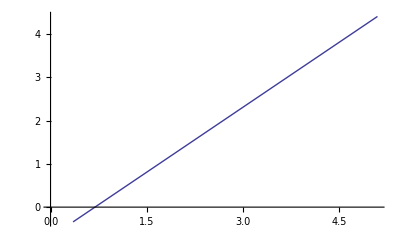

```mathematica
ListPlot[Table[B[a],{a,0.01,10,0.5}], Joined->True]
```

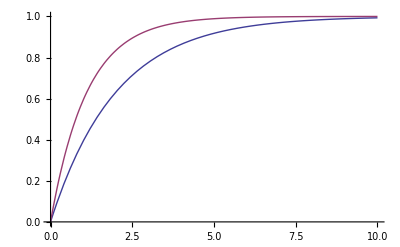

```mathematica
Plot[{m[Q[[1]], b],m[Q[[2]], b]},{b,0,10}]
```

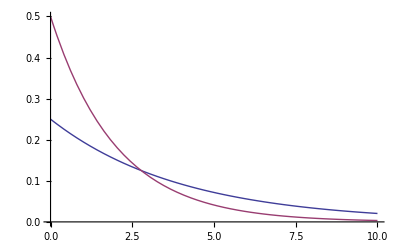

```mathematica
Plot[{mm[0.25, b],mm[0.50, b]},{b,0,10}]
```

```mathematica
Q = {0.25, 0.50};
m[q_,b_]:=1-Exp[-b*q]; 
mm[q_,b_]:=q*Exp[-b*q]; 
B[A_,Q_] := LinearSolve[{{-Q[[1]],Q[[2]]},{1,1}},{Log[Q[[2]]/Q[[1]]],A}]
```

```mathematica
B[10,Q]
```

{5.74247,4.25753}

```mathematica
q1*Exp[-q1*Log[q2/q1]/(q2-q1)]//FullSimplify
```

q1 (q2/q1)^(q1/(q1-q2))